# (Top Project - dim6 ( Ctw,Cbw,CHud ,C3phiq ) and dim 8 ( C1quWH3 , C1qdWH3 , C2q2H4D , C3 q2H4D ,CudH4D ) - Left Handed Decay width - SM , dim 6 interference )

```mathematica
Quit[]
```

```mathematica
(* Activate FA/FC *)
$LoadFeynArts=True;
$FeynCalcStartupMessages=True;
<<FeynCalc`
$FAVerbose=0;
FAPatch[PatchModelsOnly->True];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll"];
```

Successfully patched FeynArts.

```mathematica
(* Load FR model *)
InitializeModel["/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"]
```

True

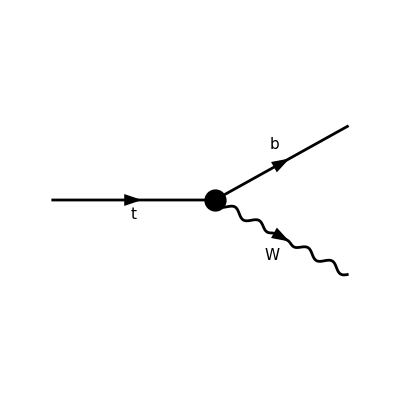

FeynArtsGraphics()(([] | Null | Null | Null | Null | Null))

```mathematica
(* Create diagrams *)
topo=CreateTopologies[0,1->2] (* # of loops = 0 *);

diag=InsertFields[topo,{F[9]}->{F[12], V[3]},InsertionLevel->{Particles},Model->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"];
Paint[diag,ColumnsXRows->{6,1},Numbering->None,SheetHeader->False,ImageSize->{800,200}]
```

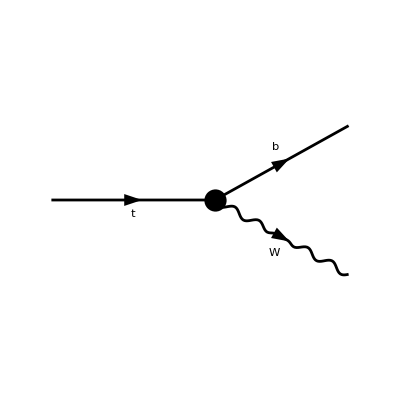

FeynArtsGraphics()(([]))

```mathematica
(* Diagram List *)
NofDiagrams=1;
lsD=Table[diag//DiagramDelete[#,Table[If[j≠i,j],{j,1,NofDiagrams}]/.Null->Sequence[]]&,{i,1,NofDiagrams}];
Paint[lsD[[1]],ColumnsXRows->{1,1},Numbering->None,SheetHeader->False,ImageSize->{200,100}]
```

```mathematica
(* Calculate amplitude *)
lsA0=Table[
FCFAConvert[CreateFeynAmp[lsD[[i]]],IncomingMomenta->{pt},OutgoingMomenta->{pb,pW},ChangeDimension->4,List->False,SMP->False,Contract->True,DropSumOver->True],
{i,1,NofDiagrams}];

lsA0=lsA0[[1]]//FeynAmpDenominatorExplicit//Simplify
(*%//TraditionalForm*)
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 gc245L Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^7+2 gc245R Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^6).(φ(OverBar[pt],FCGV(MT)))

```mathematica
gc245L = (FCGV["EL"]*(4*Lambda^4 + 2*C2q2H4D*vev^4 + C3q2H4D*vev^4 + 2*vev^4*Conjugate[C2q2H4D] + 4*Lambda^2*vev^2*Conjugate[C3phiq] - vev^4*Conjugate[C3q2H4D])*Conjugate[CKM3x3])/(4*Sqrt[2]*Lambda^4*sw);gc245R = (FCGV["EL"]*(Lambda^2*vev^2*Conjugate[CHud] + vev^4*Conjugate[CudH4D]))/(2*Sqrt[2]*Lambda^4*sw);
sw=e/g;
```

```mathematica
lsA0//FullSimplify
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(8 e Lambda^4)ⅈ δ_Col1Col2 (-4 e vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-4 e vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 √2 g Conjugate[CKM3x3] FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^7 (vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+2 Lambda^2 vev^2 Conjugate[C3phiq]+2 Lambda^4)+2 √2 g vev^2 FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 Conjugate[CHud]+vev^2 Conjugate[CudH4D])).(φ(OverBar[pt],FCGV(MT)))

```mathematica
(* Simplify *)
(* Setup the kinematics *)
SetMandelstam[s,t,u,pt,pb,pW,mpt,mpb,mpW];

rep0={EL->e,CW->cW,SW->sW,MW->mW,ME->0,MB->mb,MT->mt,
Pair[Momentum[pt],Momentum[pt]]->mt^2,
Pair[Momentum[pb],Momentum[pb]]->mb^2,
Pair[Momentum[pW],Momentum[pW]]->mW^2};
lsA=(lsA0//ReplaceAll@{FCGV[x_String]:>ToExpression[x]}(*//DiracSimplify*))/.rep0
```

-ⅈ (φ(OverBar[pb],mb)).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+(g Conjugate[CKM3x3] (γ̄·(ε̄)^*(pW)).(γ̄)^7 (2 vev^4 Conjugate[C2q2H4D]+2 C2q2H4D vev^4+4 Lambda^2 vev^2 Conjugate[C3phiq]-vev^4 Conjugate[C3q2H4D]+C3q2H4D vev^4+4 Lambda^4))/(2 √2)+(g (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 vev^2 Conjugate[CHud]+vev^4 Conjugate[CudH4D]))/(√2)).(φ(OverBar[pt],mt))

```mathematica
Fspin[x_]:=x//SUNFDeltaContract//FermionSpinSum[#,ExtraFactor->1/2]&//ReplaceAll[#,DiracTrace->TR]&
(lsAsq=(lsA*ComplexConjugate[lsA])//Simplify//Fspin//Contract)
```

```mathematica
lsAsqq=lsAsq/.{SUNN->Nc}//FullSimplify
```

1/(32 Lambda^8)Nc (4 g^2 Lambda^4 (Conjugate[CHud])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+8 g Lambda^2 Conjugate[CHud] (g Conjugate[CudH4D] (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+√2 mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev+mb Conjugate[CKM3x3] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))) vev^2+4 mb Conjugate[CKM3x3] (2 g Conjugate[CudH4D] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev^3+Conjugate[C1qdWH3] (-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-4 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) vev^2+4 Lambda^2 Conjugate[CbW] (-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-2 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev+4 (g^2 (Conjugate[CudH4D])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^8+2 √2 g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2 (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-ⅈ (((ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))-ⅈ ((OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW)))) OverBar[pW]^2-(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)))+((OverBar[pb]·OverBar[pt]) OverBar[pW]^2-2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW])) ((ε̄)^*(pW)·ε̄(pW))))+(Conjugate[CKM3x3])^2 (-16 g^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-64 √2 CtW g mt vev (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-16 ⅈ g^2 vev^4 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 √2 C1quWH3 g mt vev^3 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-64 √2 CtW g mt vev^3 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-256 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 g^2 vev^4 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^4-128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C3q2H4D CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C1quWH3 g mt vev^5 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-256 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2-64 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2+32 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D) Lambda^2-32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+4 C2q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-3 C3q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-4 g^2 vev^8 (Conjugate[C2q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-g^2 vev^8 (Conjugate[C3q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-16 ⅈ √2 C1quWH3 g mt vev^7 Im(C3q2H4D) (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))-64 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW))-16 C2q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-16 ⅈ g^2 vev^8 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-32 √2 C1quWH3 g mt vev^7 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 ⅈ vev (2 CtW Lambda^2+C1quWH3 vev^2) (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (4 vev (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW])+√2 g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))+4 C3q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D)+(OverBar[pb]·ε̄(pW)) ((OverBar[pt]·(ε̄)^*(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·(ε̄)^*(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))+(OverBar[pb]·(ε̄)^*(pW)) ((OverBar[pt]·ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·ε̄(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))))

1/(32 Lambda^8)Nc (4 g^2 Lambda^4 (Conjugate[CHud])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+8 g Lambda^2 Conjugate[CHud] (g Conjugate[CudH4D] (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+√2 mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev+mb Conjugate[CKM3x3] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))) vev^2+

```mathematica
(1/(32 Lambda^8))*Nc*(4 g^2 Lambda^4 Conjugate[CHud]^2*(I LeviCivitaContraction[pb,pt,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[pb,pt]*MinkSP[Epclh,Eplh])*vev^4+8 g Lambda^2 Conjugate[CHud]*(g Conjugate[CudH4D]*(I LeviCivitaContraction[pb,pt,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[pb,pt]*MinkSP[Epclh,Eplh])*vev^4+Sqrt[2]*mt*(2 Conjugate[CbW]*Lambda^2+vev^2*Conjugate[C1qdWH3])*(2 I LeviCivitaContraction[pb,pW,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pW,Epclh]+MinkSP[pb,Epclh]*MinkSP[pW,Eplh]-2 MinkSP[pb,pW]*MinkSP[Epclh,Eplh])*vev+mb*Conjugate[CKM3x3]*(I Sqrt[2]*vev*(2 CtW*Lambda^2+C1quWH3*vev^2)*(2 LeviCivitaContraction[pt,pW,Epclh,Eplh]+I (MinkSP[pt,Eplh]*MinkSP[pW,Epclh]+MinkSP[pt,Epclh]*MinkSP[pW,Eplh]))+MinkSP[Epclh,Eplh]*(2 g Lambda^2*mt*Conjugate[C3phiq]*vev^2+2 Sqrt[2]*(2 CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[pt,pW]*vev+g*mt*(2 Lambda^4+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))*vev^2+
```

4 mb Conjugate[CKM3x3] (2 g Conjugate[CudH4D] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev^3+Conjugate[C1qdWH3] (-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-4 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-

```mathematica
4 mb Conjugate[CKM3x3]*(2 g Conjugate[CudH4D]*(I Sqrt[2] vev (2 CtW Lambda^2+C1quWH3 vev^2)*(2 LeviCivitaContraction[pt,pW,Epclh,Eplh]+I (MinkSP[pt,Eplh]*MinkSP[pW,Epclh]+MinkSP[pt,Epclh]*MinkSP[pW,Eplh]))+MinkSP[Epclh,Eplh]*(2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[pt,pW] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev^3+Conjugate[C1qdWH3]*(-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[pW,Epclh]*MinkSP[pW,Eplh]-MinkSP[pW,pW]*MinkSP[Epclh,Eplh])-4 I Sqrt[2] g LeviCivitaContraction[pt,pW,Epclh,Eplh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2 Sqrt[2] g*(MinkSP[pt,Epclh]*MinkSP[pW,Eplh]-2 MinkSP[pt,pW]*MinkSP[Epclh,Eplh])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-
```

2 √2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) vev^2+4 Lambda^2 Conjugate[CbW] (-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-2 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev+

```mathematica
2 Sqrt[2] g MinkSP[pt,Eplh] MinkSP[pW,Epclh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))*vev^2
+4 Lambda^2 Conjugate[CbW]*(-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[pW,Epclh]*MinkSP[pW,Eplh]-MinkSP[pW,pW]*MinkSP[Epclh,Eplh])-2 I Sqrt[2] g LeviCivitaContraction[pt,pW,Epclh,Eplh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g MinkSP[pt,Eplh]*MinkSP[pW,Epclh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g*(MinkSP[pt,Epclh]*MinkSP[pW,Eplh]-2 MinkSP[pt,pW]*MinkSP[Epclh,Eplh])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev+
```

4 (g^2 (Conjugate[CudH4D])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^8+2 √2 g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2 (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-ⅈ (((ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))-ⅈ ((OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW)))) OverBar[pW]^2-(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)))+((OverBar[pb]·OverBar[pt]) OverBar[pW]^2-2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW])) ((ε̄)^*(pW)·ε̄(pW))))+

```mathematica
4 (g^2 Conjugate[CudH4D]^2*(I LeviCivitaContraction[pb,pt,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[pb,pt]*MinkSP[Epclh,Eplh])*vev^8+2 Sqrt[2] g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3])*Conjugate[CudH4D]*(2 I LeviCivitaContraction[pb,pW,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pW,Epclh]+MinkSP[pb,Epclh]*MinkSP[pW,Eplh]-2 MinkSP[pb,pW]*MinkSP[Epclh,Eplh])*vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2*(2 I LeviCivitaContraction[pb,pW,Epclh,Eplh]*MinkSP[pt,pW]+MinkSP[pb,Eplh]*MinkSP[pW,Epclh]*MinkSP[pt,pW]+MinkSP[pb,Epclh]*MinkSP[pW,Eplh]*MinkSP[pt,pW]+MinkSP[pb,pW]*MinkSP[pt,Eplh]*MinkSP[pW,Epclh]+MinkSP[pb,pW]*MinkSP[pt,Epclh]*MinkSP[pW,Eplh]-MinkSP[pb,pt]*MinkSP[pW,Epclh]*MinkSP[pW,Eplh]-I ((LeviCivitaContraction[pb,pt,Epclh,Eplh]-I (MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]))*MinkSP[pW,pW]-LeviCivitaContraction[pb,pt,pW,Eplh]*MinkSP[pW,Epclh]+LeviCivitaContraction[pb,pt,pW,Epclh]*MinkSP[pW,Eplh])+(MinkSP[pb,pt]*MinkSP[pW,pW]-2 MinkSP[pb,pW]*MinkSP[pt,pW])*MinkSP[Epclh,Eplh]))+
```

(Conjugate[CKM3x3])^2 (-16 g^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-64 √2 CtW g mt vev (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-16 ⅈ g^2 vev^4 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 √2 C1quWH3 g mt vev^3 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-64 √2 CtW g mt vev^3 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-256 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4+

```mathematica
Conjugate[CKM3x3]^2*(-16 g^2 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^6-64 Sqrt[2] CtW g mt vev MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^6-128 I CtW^2 vev^2 LeviCivitaContraction[pb,pt,pW,Eplh] MinkSP[pW,Epclh] Lambda^4+128 CtW^2 vev^2 MinkSP[pb,pW] MinkSP[pt,Eplh] MinkSP[pW,Epclh] Lambda^4+128 I CtW^2 vev^2 LeviCivitaContraction[pb,pt,pW,Epclh] MinkSP[pW,Eplh] Lambda^4+128 CtW^2 vev^2 MinkSP[pb,pW] MinkSP[pt,Epclh] MinkSP[pW,Eplh] Lambda^4-128 CtW^2 vev^2 MinkSP[pb,pt] MinkSP[pW,Epclh] MinkSP[pW,Eplh] Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^4-16 I g^2 vev^4 Im[C3q2H4D] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^4-32 Sqrt[2] C1quWH3 g mt vev^3 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^4-64 Sqrt[2] CtW g mt vev^3 Conjugate[C3phiq] MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^4-256 CtW^2 vev^2 MinkSP[pb,pW] MinkSP[pt,pW] MinkSP[Epclh,Eplh] Lambda^4+
```

128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 g^2 vev^4 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^4-128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C3q2H4D CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C1quWH3 g mt vev^5 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-256 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2-64 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2+

```mathematica
128 CtW^2 vev^2 MinkSP[pb,pt] MinkSP[pW,pW] MinkSP[Epclh,Eplh] Lambda^4-32 g^2 vev^4 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^4-128 I C1quWH3 CtW vev^4 LeviCivitaContraction[pb,pt,pW,Eplh] MinkSP[pW,Epclh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[pb,pW] MinkSP[pt,Eplh] MinkSP[pW,Epclh] Lambda^2+128 I C1quWH3 CtW vev^4 LeviCivitaContraction[pb,pt,pW,Epclh] MinkSP[pW,Eplh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[pb,pW] MinkSP[pt,Epclh] MinkSP[pW,Eplh] Lambda^2-128 C1quWH3 CtW vev^4 MinkSP[pb,pt] MinkSP[pW,Epclh] MinkSP[pW,Eplh] Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^2-32 Sqrt[2] C3q2H4D CtW g mt vev^5 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^2-32 Sqrt[2] C1quWH3 g mt vev^5 Conjugate[C3phiq] MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^2-256 C1quWH3 CtW vev^4 MinkSP[pb,pW] MinkSP[pt,pW] MinkSP[Epclh,Eplh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[pb,pt] MinkSP[pW,pW] MinkSP[Epclh,Eplh] Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^2-64 Sqrt[2] CtW g mt vev^5 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^2+
```

32 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D) Lambda^2-32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+4 C2q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-3 C3q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-4 g^2 vev^8 (Conjugate[C2q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-g^2 vev^8 (Conjugate[C3q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-16 ⅈ √2 C1quWH3 g mt vev^7 Im(C3q2H4D) (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))-64 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW))-16 C2q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-16 ⅈ g^2 vev^8 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-32 √2 C1quWH3 g mt vev^7 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-

```mathematica
32 Sqrt[2] CtW g mt vev^5 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Re[C3q2H4D] Lambda^2-32 I C1quWH3^2 vev^6 LeviCivitaContraction[pb,pt,pW,Eplh] MinkSP[pW,Epclh]+32 C1quWH3^2 vev^6 MinkSP[pb,pW] MinkSP[pt,Eplh] MinkSP[pW,Epclh]+32 I C1quWH3^2 vev^6 LeviCivitaContraction[pb,pt,pW,Epclh] MinkSP[pW,Eplh]+32 C1quWH3^2 vev^6 MinkSP[pb,pW] MinkSP[pt,Epclh] MinkSP[pW,Eplh]-32 C1quWH3^2 vev^6 MinkSP[pb,pt] MinkSP[pW,Epclh] MinkSP[pW,Eplh]+4 C2q2H4D^2 g^2 vev^8 MinkSP[pb,pt] MinkSP[Epclh,Eplh]-3 C3q2H4D^2 g^2 vev^8 MinkSP[pb,pt] MinkSP[Epclh,Eplh]-4 g^2 vev^8 Conjugate[C2q2H4D]^2 MinkSP[pb,pt] MinkSP[Epclh,Eplh]-g^2 vev^8 Conjugate[C3q2H4D]^2 MinkSP[pb,pt] MinkSP[Epclh,Eplh]-16 I Sqrt[2] C1quWH3 g mt vev^7 Im[C3q2H4D] MinkSP[pb,pW] MinkSP[Epclh,Eplh]-64 C1quWH3^2 vev^6 MinkSP[pb,pW] MinkSP[pt,pW] MinkSP[Epclh,Eplh]+32 C1quWH3^2 vev^6 MinkSP[pb,pt] MinkSP[pW,pW] MinkSP[Epclh,Eplh]-16 C2q2H4D g^2 vev^8 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C2q2H4D]-16 I g^2 vev^8 Im[C3q2H4D] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C2q2H4D]-32 Sqrt[2] C1quWH3 g mt vev^7 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Re[C2q2H4D]-
```

ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 ⅈ vev (2 CtW Lambda^2+C1quWH3 vev^2) (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (4 vev (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW])+√2 g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))+

```mathematica
I LeviCivitaContraction[pb,pt,Epclh,Eplh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[pW,pW]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 I vev (2 CtW Lambda^2+C1quWH3 vev^2)*LeviCivitaContraction[pb,pW,Epclh,Eplh]*(4 vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[pt,pW]+Sqrt[2] g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+
```

4 C3q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D)+(OverBar[pb]·ε̄(pW)) ((OverBar[pt]·(ε̄)^*(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·(ε̄)^*(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))+

```mathematica
4 C3q2H4D g^2 vev^8 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C3q2H4D]+MinkSP[pb,Eplh]*(MinkSP[pt,Epclh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[pW,pW]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[pW,Epclh]*(4 vev MinkSP[pt,pW] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))+
```

(OverBar[pb]·(ε̄)^*(pW)) ((OverBar[pt]·ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·ε̄(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))))

```mathematica
MinkSP[pb,Epclh]*(MinkSP[pt,Eplh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[pW,pW])*vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[pW,Eplh]*(4 vev MinkSP[pt,pW] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))))
```

```mathematica
Quit[]
```

```mathematica
Pb={Eb,pb Sin[θ]Cos[ϕ],pb Sin[θ] Sin[ϕ],pb Cos[θ]};
Pw={EW,-pb Sin[θ]Cos[ϕ],-pb Sin[θ] Sin[ϕ],-pb Cos[θ]};
Pt={mt,0,0,0};
Epl=1/(mw){pw,-EW Sin[θ]Cos[ϕ],-EW Sin[θ] Sin[ϕ],-EW Cos[θ]};
```

```mathematica
MinkSP[vec1_,vec2_]:=Times[vec1[[1]],vec2[[1]]]-Times[vec1[[2]],vec2[[2]]]-Times[vec1[[3]],vec2[[3]]]-Times[vec1[[4]],vec2[[4]]]
```

```mathematica
(*Define Levi-Civita with provided function, (-1)for lower index of Levi-Civita *)
LeviCivita[indices__]:=-Module[{list={indices}},If[Length[list]≠4||DuplicateFreeQ[list]===False,0,Signature[list]]]
(*Contraction of Levi-Civita with 4 specific 4-vectors*)
LeviCivitaContraction[Pb_,pt_,Epclh_,Eplh_]:=Sum[LeviCivita[mu,nu,rho,sigma]*Pb[[mu+1]] pt[[nu+1]] Epclh[[rho+1]]*Eplh[[sigma+1]],{mu,0,3},{nu,0,3},{rho,0,3},{sigma,0,3}]//Simplify
```

```mathematica
Msqt=(1/(32 Lambda^8))*Nc*(4 g^2 Lambda^4 Conjugate[CHud]^2*(I LeviCivitaContraction[Pb,Pt,Epl,Epl]+MinkSP[Pb,Epl]*MinkSP[Pt,Epl]+MinkSP[Pb,Epl]*MinkSP[Pt,Epl]-MinkSP[Pb,Pt]*MinkSP[Epl,Epl])*vev^4+8 g Lambda^2 Conjugate[CHud]*(g Conjugate[CudH4D]*(I LeviCivitaContraction[Pb,Pt,Epl,Epl]+MinkSP[Pb,Epl]*MinkSP[Pt,Epl]+MinkSP[Pb,Epl]*MinkSP[Pt,Epl]-MinkSP[Pb,Pt]*MinkSP[Epl,Epl])*vev^4+Sqrt[2]*mt*(2 Conjugate[CbW]*Lambda^2+vev^2*Conjugate[C1qdWH3])*(2 I LeviCivitaContraction[Pb,Pw,Epl,Epl]+MinkSP[Pb,Epl]*MinkSP[Pw,Epl]+MinkSP[Pb,Epl]*MinkSP[Pw,Epl]-2 MinkSP[Pb,Pw]*MinkSP[Epl,Epl])*vev+mb*Conjugate[CKM3x3]*(I Sqrt[2]*vev*(2 CtW*Lambda^2+C1quWH3*vev^2)*(2 LeviCivitaContraction[Pt,Pw,Epl,Epl]+I (MinkSP[Pt,Epl]*MinkSP[Pw,Epl]+MinkSP[Pt,Epl]*MinkSP[Pw,Epl]))+MinkSP[Epl,Epl]*(2 g Lambda^2*mt*Conjugate[C3phiq]*vev^2+2 Sqrt[2]*(2 CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[Pt,Pw]*vev+g*mt*(2 Lambda^4+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))*vev^2+4 mb Conjugate[CKM3x3]*(2 g Conjugate[CudH4D]*(I Sqrt[2] vev (2 CtW Lambda^2+C1quWH3 vev^2)*(2 LeviCivitaContraction[Pt,Pw,Epl,Epl]+I (MinkSP[Pt,Epl]*MinkSP[Pw,Epl]+MinkSP[Pt,Epl]*MinkSP[Pw,Epl]))+MinkSP[Epl,Epl]*(2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev^3+Conjugate[C1qdWH3]*(-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[Pw,Epl]*MinkSP[Pw,Epl]-MinkSP[Pw,Pw]*MinkSP[Epl,Epl])-4 I Sqrt[2] g LeviCivitaContraction[Pt,Pw,Epl,Epl]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2 Sqrt[2] g*(MinkSP[Pt,Epl]*MinkSP[Pw,Epl]-2 MinkSP[Pt,Pw]*MinkSP[Epl,Epl])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2 Sqrt[2] g MinkSP[Pt,Epl] MinkSP[Pw,Epl]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))*vev^2+4 Lambda^2 Conjugate[CbW]*(-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[Pw,Epl]*MinkSP[Pw,Epl]-MinkSP[Pw,Pw]*MinkSP[Epl,Epl])-2 I Sqrt[2] g LeviCivitaContraction[Pt,Pw,Epl,Epl]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g MinkSP[Pt,Epl]*MinkSP[Pw,Epl]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g*(MinkSP[Pt,Epl]*MinkSP[Pw,Epl]-2 MinkSP[Pt,Pw]*MinkSP[Epl,Epl])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev+4 (g^2 Conjugate[CudH4D]^2*(I LeviCivitaContraction[Pb,Pt,Epl,Epl]+MinkSP[Pb,Epl]*MinkSP[Pt,Epl]+MinkSP[Pb,Epl]*MinkSP[Pt,Epl]-MinkSP[Pb,Pt]*MinkSP[Epl,Epl])*vev^8+2 Sqrt[2] g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3])*Conjugate[CudH4D]*(2 I LeviCivitaContraction[Pb,Pw,Epl,Epl]+MinkSP[Pb,Epl]*MinkSP[Pw,Epl]+MinkSP[Pb,Epl]*MinkSP[Pw,Epl]-2 MinkSP[Pb,Pw]*MinkSP[Epl,Epl])*vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2*(2 I LeviCivitaContraction[Pb,Pw,Epl,Epl]*MinkSP[Pt,Pw]+MinkSP[Pb,Epl]*MinkSP[Pw,Epl]*MinkSP[Pt,Pw]+MinkSP[Pb,Epl]*MinkSP[Pw,Epl]*MinkSP[Pt,Pw]+MinkSP[Pb,Pw]*MinkSP[Pt,Epl]*MinkSP[Pw,Epl]+MinkSP[Pb,Pw]*MinkSP[Pt,Epl]*MinkSP[Pw,Epl]-MinkSP[Pb,Pt]*MinkSP[Pw,Epl]*MinkSP[Pw,Epl]-I ((LeviCivitaContraction[Pb,Pt,Epl,Epl]-I (MinkSP[Pb,Epl]*MinkSP[Pt,Epl]+MinkSP[Pb,Epl]*MinkSP[Pt,Epl]))*MinkSP[Pw,Pw]-LeviCivitaContraction[Pb,Pt,Pw,Epl]*MinkSP[Pw,Epl]+LeviCivitaContraction[Pb,Pt,Pw,Epl]*MinkSP[Pw,Epl])+(MinkSP[Pb,Pt]*MinkSP[Pw,Pw]-2 MinkSP[Pb,Pw]*MinkSP[Pt,Pw])*MinkSP[Epl,Epl]))+Conjugate[CKM3x3]^2*(-16 g^2 MinkSP[Pb,Pt] MinkSP[Epl,Epl] Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epl,Epl] Lambda^6-64 Sqrt[2] CtW g mt vev MinkSP[Pb,Pw] MinkSP[Epl,Epl] Lambda^6-128 I CtW^2 vev^2 LeviCivitaContraction[Pb,Pt,Pw,Epl] MinkSP[Pw,Epl] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Epl] MinkSP[Pw,Epl] Lambda^4+128 I CtW^2 vev^2 LeviCivitaContraction[Pb,Pt,Pw,Epl] MinkSP[Pw,Epl] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Epl] MinkSP[Pw,Epl] Lambda^4-128 CtW^2 vev^2 MinkSP[Pb,Pt] MinkSP[Pw,Epl] MinkSP[Pw,Epl] Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 MinkSP[Pb,Pt] MinkSP[Epl,Epl] Lambda^4-16 I g^2 vev^4 Im[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epl,Epl] Lambda^4-32 Sqrt[2] C1quWH3 g mt vev^3 MinkSP[Pb,Pw] MinkSP[Epl,Epl] Lambda^4-64 Sqrt[2] CtW g mt vev^3 Conjugate[C3phiq] MinkSP[Pb,Pw] MinkSP[Epl,Epl] Lambda^4-256 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epl,Epl] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epl,Epl] Lambda^4-32 g^2 vev^4 MinkSP[Pb,Pt] MinkSP[Epl,Epl] Re[C2q2H4D] Lambda^4-128 I C1quWH3 CtW vev^4 LeviCivitaContraction[Pb,Pt,Pw,Epl] MinkSP[Pw,Epl] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Epl] MinkSP[Pw,Epl] Lambda^2+128 I C1quWH3 CtW vev^4 LeviCivitaContraction[Pb,Pt,Pw,Epl] MinkSP[Pw,Epl] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Epl] MinkSP[Pw,Epl] Lambda^2-128 C1quWH3 CtW vev^4 MinkSP[Pb,Pt] MinkSP[Pw,Epl] MinkSP[Pw,Epl] Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epl,Epl] Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epl,Epl] Lambda^2-32 Sqrt[2] C3q2H4D CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epl,Epl] Lambda^2-32 Sqrt[2] C1quWH3 g mt vev^5 Conjugate[C3phiq] MinkSP[Pb,Pw] MinkSP[Epl,Epl] Lambda^2-256 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epl,Epl] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epl,Epl] Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epl,Epl] Re[C2q2H4D] Lambda^2-64 Sqrt[2] CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epl,Epl] Re[C2q2H4D] Lambda^2+32 Sqrt[2] CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epl,Epl] Re[C3q2H4D] Lambda^2-32 I C1quWH3^2 vev^6 LeviCivitaContraction[Pb,Pt,Pw,Epl] MinkSP[Pw,Epl]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Epl] MinkSP[Pw,Epl]+32 I C1quWH3^2 vev^6 LeviCivitaContraction[Pb,Pt,Pw,Epl] MinkSP[Pw,Epl]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Epl] MinkSP[Pw,Epl]-32 C1quWH3^2 vev^6 MinkSP[Pb,Pt] MinkSP[Pw,Epl] MinkSP[Pw,Epl]+4 C2q2H4D^2 g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epl,Epl]-3 C3q2H4D^2 g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epl,Epl]-4 g^2 vev^8 Conjugate[C2q2H4D]^2 MinkSP[Pb,Pt] MinkSP[Epl,Epl]-g^2 vev^8 Conjugate[C3q2H4D]^2 MinkSP[Pb,Pt] MinkSP[Epl,Epl]-16 I Sqrt[2] C1quWH3 g mt vev^7 Im[C3q2H4D] MinkSP[Pb,Pw] MinkSP[Epl,Epl]-64 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epl,Epl]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epl,Epl]-16 C2q2H4D g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epl,Epl] Re[C2q2H4D]-16 I g^2 vev^8 Im[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epl,Epl] Re[C2q2H4D]-32 Sqrt[2] C1quWH3 g mt vev^7 MinkSP[Pb,Pw] MinkSP[Epl,Epl] Re[C2q2H4D]-I LeviCivitaContraction[Pb,Pt,Epl,Epl]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 I vev (2 CtW Lambda^2+C1quWH3 vev^2)*LeviCivitaContraction[Pb,Pw,Epl,Epl]*(4 vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw]+Sqrt[2] g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+4 C3q2H4D g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epl,Epl] Re[C3q2H4D]+MinkSP[Pb,Epl]*(MinkSP[Pt,Epl]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[Pw,Epl]*(4 vev MinkSP[Pt,Pw] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))+MinkSP[Pb,Epl]*(MinkSP[Pt,Epl]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw])*vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[Pw,Epl]*(4 vev MinkSP[Pt,Pw] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))))//FullSimplify
```

1/(32 Lambda^8 mw^2)mt Nc (32 Eb (EW^2-pb pw)^2 vev^6 Conjugate[C1qdWH3]^2+128 Eb Lambda^4 (EW^2-pb pw)^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 (2 EW pb pw+Eb (EW^2+pw^2)) vev^4 Conjugate[CHud]^2+4 g^2 (2 EW pb pw+Eb (EW^2+pw^2)) vev^8 Conjugate[CudH4D]^2-8 g Lambda^2 vev^2 Conjugate[CHud] (-g (2 EW pb pw+Eb (EW^2+pw^2)) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 √2 EW^3 vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 √2 EW pb pw vev (2 CtW Lambda^2+C1quWH3 vev^2)+EW^2 g (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)-g pw^2 (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g (EW-pw) (EW+pw) vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+32 Lambda^2 (EW^2-pb pw) vev Conjugate[CbW] (-4 mb (EW^2-pb pw) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (Eb EW+pb pw) vev^2 Conjugate[CHud]+(Eb EW+pb pw) vev^4 Conjugate[CudH4D]-EW mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+16 (EW^2-pb pw) vev^3 Conjugate[C1qdWH3] (8 Eb Lambda^2 (EW^2-pb pw) vev Conjugate[CbW]-4 mb (EW^2-pb pw) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (Eb EW+pb pw) vev^2 Conjugate[CHud]+(Eb EW+pb pw) vev^4 Conjugate[CudH4D]-EW mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-8 g mb vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (2 √2 EW^3 vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 √2 EW pb pw vev (2 CtW Lambda^2+C1quWH3 vev^2)+EW^2 g (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)-g pw^2 (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g (EW-pw) (EW+pw) vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D])))+Conjugate[CKM3x3]^2 (16 g^2 Lambda^8 (2 EW pb pw+Eb (EW^2+pw^2))+64 √2 CtW g Lambda^6 (EW^2-pb pw) (Eb EW+pb pw) vev+4 g^2 (2 EW pb pw+Eb (EW^2+pw^2)) vev^8 Conjugate[C2q2H4D]^2+32 √2 g Lambda^4 (EW^2-pb pw) (Eb EW+pb pw) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])+8 g^2 (2 EW pb pw+Eb (EW^2+pw^2)) vev^6 Conjugate[C2q2H4D] (C2q2H4D vev^2+2 Lambda^2 Conjugate[C3phiq])+32 Lambda^4 vev^2 (4 CtW^2 Eb (EW^2-pb pw)^2+g^2 Lambda^2 (2 EW pb pw+Eb (EW^2+pw^2)) Conjugate[C3phiq])+8 vev^6 (4 C1quWH3^2 Eb (EW^2-pb pw)^2+2 g^2 Lambda^2 (2 EW pb pw+Eb (EW^2+pw^2)) Conjugate[C3phiq] (C2q2H4D+C3q2H4D-Re[C3q2H4D]))+32 √2 g Lambda^2 (EW^2-pb pw) (Eb EW+pb pw) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^2 vev^4 (8 C1quWH3 CtW Eb (EW^2-pb pw)^2+g^2 Lambda^2 (2 EW pb pw+Eb (EW^2+pw^2)) (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+16 √2 C1quWH3 g (EW^2-pb pw) (Eb EW+pb pw) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+g^2 vev^8 (4 C2q2H4D^2 (2 EW pb pw+Eb (EW^2+pw^2))+C3q2H4D^2 (6 EW pb pw+Eb (EW^2+pw^2))-2 C3q2H4D Eb (EW^2+pw^2) Conjugate[C3q2H4D]+(2 EW pb pw+Eb (EW^2+pw^2)) Conjugate[C3q2H4D]^2+8 Re[C2q2H4D] (2 ⅈ Eb (EW^2+pw^2) Im[C3q2H4D]+4 EW pb pw (C3q2H4D-Re[C3q2H4D]))-8 C3q2H4D EW pb pw Re[C3q2H4D])))

```mathematica
EW=(mt^2+mw^2-mb^2)/(2 mt);
Eb=mt-EW;
pw=pb;
pb=(1/(2 mt)) Sqrt[mt^2 - (mb + mw)^2] Sqrt[mt^2 - (mb - mw)^2];
```

```mathematica
Msqtotal=1/(32 Lambda^8 mw^2)mt Nc (32 Eb (EW^2-pb pw)^2 vev^6 Conjugate[C1qdWH3]^2+128 Eb Lambda^4 (EW^2-pb pw)^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 (2 EW pb pw+Eb (EW^2+pw^2)) vev^4 Conjugate[CHud]^2+4 g^2 (2 EW pb pw+Eb (EW^2+pw^2)) vev^8 Conjugate[CudH4D]^2-8 g Lambda^2 vev^2 Conjugate[CHud] (-g (2 EW pb pw+Eb (EW^2+pw^2)) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 √2 EW^3 vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 √2 EW pb pw vev (2 CtW Lambda^2+C1quWH3 vev^2)+EW^2 g (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)-g pw^2 (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g (EW-pw) (EW+pw) vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+32 Lambda^2 (EW^2-pb pw) vev Conjugate[CbW] (-4 mb (EW^2-pb pw) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (Eb EW+pb pw) vev^2 Conjugate[CHud]+(Eb EW+pb pw) vev^4 Conjugate[CudH4D]-EW mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+16 (EW^2-pb pw) vev^3 Conjugate[C1qdWH3] (8 Eb Lambda^2 (EW^2-pb pw) vev Conjugate[CbW]-4 mb (EW^2-pb pw) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (Eb EW+pb pw) vev^2 Conjugate[CHud]+(Eb EW+pb pw) vev^4 Conjugate[CudH4D]-EW mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-8 g mb vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (2 √2 EW^3 vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 √2 EW pb pw vev (2 CtW Lambda^2+C1quWH3 vev^2)+EW^2 g (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)-g pw^2 (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g (EW-pw) (EW+pw) vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D])))+Conjugate[CKM3x3]^2 (16 g^2 Lambda^8 (2 EW pb pw+Eb (EW^2+pw^2))+64 √2 CtW g Lambda^6 (EW^2-pb pw) (Eb EW+pb pw) vev+4 g^2 (2 EW pb pw+Eb (EW^2+pw^2)) vev^8 Conjugate[C2q2H4D]^2+32 √2 g Lambda^4 (EW^2-pb pw) (Eb EW+pb pw) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])+8 g^2 (2 EW pb pw+Eb (EW^2+pw^2)) vev^6 Conjugate[C2q2H4D] (C2q2H4D vev^2+2 Lambda^2 Conjugate[C3phiq])+32 Lambda^4 vev^2 (4 CtW^2 Eb (EW^2-pb pw)^2+g^2 Lambda^2 (2 EW pb pw+Eb (EW^2+pw^2)) Conjugate[C3phiq])+8 vev^6 (4 C1quWH3^2 Eb (EW^2-pb pw)^2+2 g^2 Lambda^2 (2 EW pb pw+Eb (EW^2+pw^2)) Conjugate[C3phiq] (C2q2H4D+C3q2H4D-Re[C3q2H4D]))+32 √2 g Lambda^2 (EW^2-pb pw) (Eb EW+pb pw) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^2 vev^4 (8 C1quWH3 CtW Eb (EW^2-pb pw)^2+g^2 Lambda^2 (2 EW pb pw+Eb (EW^2+pw^2)) (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+16 √2 C1quWH3 g (EW^2-pb pw) (Eb EW+pb pw) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+g^2 vev^8 (4 C2q2H4D^2 (2 EW pb pw+Eb (EW^2+pw^2))+C3q2H4D^2 (6 EW pb pw+Eb (EW^2+pw^2))-2 C3q2H4D Eb (EW^2+pw^2) Conjugate[C3q2H4D]+(2 EW pb pw+Eb (EW^2+pw^2)) Conjugate[C3q2H4D]^2+8 Re[C2q2H4D] (2 ⅈ Eb (EW^2+pw^2) Im[C3q2H4D]+4 EW pb pw (C3q2H4D-Re[C3q2H4D]))-8 C3q2H4D EW pb pw Re[C3q2H4D])))//FullSimplify
```

1/(64 Lambda^8 mw^2)Nc (32 mw^4 (mb^2+mt^2-mw^2) vev^6 Conjugate[C1qdWH3]^2+128 Lambda^4 mw^4 (mb^2+mt^2-mw^2) vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^4 Conjugate[CHud]^2+4 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^8 Conjugate[CudH4D]^2-8 g Lambda^2 vev^2 Conjugate[CHud] (g (-(mb^2-mt^2)^2+(mb^2+mt^2) mw^2) vev^4 Conjugate[CudH4D]+2 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+16 mw^2 vev^3 Conjugate[C1qdWH3] (8 Lambda^2 mw^2 (mb^2+mt^2-mw^2) vev Conjugate[CbW]-8 mb mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]-√2 g (Lambda^2 mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]-mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-32 Lambda^2 mw^2 vev Conjugate[CbW] (8 mb mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]-mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 g mb mw^2 vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D])))-Conjugate[CKM3x3]^2 (-16 g^2 Lambda^8 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2)+64 √2 CtW g Lambda^6 mt mw^2 (mb^2-mt^2+mw^2) vev-4 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^8 Conjugate[C2q2H4D]^2+32 √2 g Lambda^4 mt mw^2 (mb^2-mt^2+mw^2) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])-8 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^6 Conjugate[C2q2H4D] (C2q2H4D vev^2+2 Lambda^2 Conjugate[C3phiq])-32 Lambda^4 vev^2 (4 CtW^2 mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Conjugate[C3phiq])-16 vev^6 (2 C1quWH3^2 mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Conjugate[C3phiq] (C2q2H4D+C3q2H4D-Re[C3q2H4D]))+32 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^2 vev^4 (8 C1quWH3 CtW mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+16 √2 C1quWH3 g mt mw^2 (mb^2-mt^2+mw^2) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+g^2 vev^8 (-((4 C2q2H4D^2+3 C3q2H4D^2) (mb^2-mt^2)^2)+(4 C2q2H4D^2+C3q2H4D^2) (mb^2+mt^2) mw^2-2 C3q2H4D (mb^2+mt^2) mw^2 Conjugate[C3q2H4D]+(-(mb^2-mt^2)^2+(mb^2+mt^2) mw^2) Conjugate[C3q2H4D]^2-16 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Re[C2q2H4D] (C3q2H4D-Re[C3q2H4D])+4 C3q2H4D (mb^2-mt^2)^2 Re[C3q2H4D])))

```mathematica
(*Compute decay width systematically*)
```

```mathematica
(*Define p*for the decay t->W+b*)
phaseSpacePrefactor[m1_,m2_,M_]:=1/(2 M) Sqrt[M^2-(m1+m2)^2] Sqrt[M^2-(m1-m2)^2];
pStar=phaseSpacePrefactor[mw,mb,mt];
(*Define two-body phase space integral with p*substitution*)
dPhaseSpace=(1/(32 Pi^2 mt^2))*pStar;
DecayWidth0=Integrate[Msqtotal *dPhaseSpace*Sin[θ],{θ,0,Pi},{phi,0,2 Pi}]/.{pb->pStar,Eb->(mb^2-mw^2+mt^2)/(2mt)}//FullSimplify
```

```mathematica
1/(1024 Lambda^8 mt^3 mw^2 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (32 mw^4 (mb^2+mt^2-mw^2) vev^6 Conjugate[C1qdWH3]^2+128 Lambda^4 mw^4 (mb^2+mt^2-mw^2) vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^4 Conjugate[CHud]^2+4 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^8 Conjugate[CudH4D]^2-8 g Lambda^2 vev^2 Conjugate[CHud] (g (-(mb^2-mt^2)^2+(mb^2+mt^2) mw^2) vev^4 Conjugate[CudH4D]+2 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+16 mw^2 vev^3 Conjugate[C1qdWH3] (8 Lambda^2 mw^2 (mb^2+mt^2-mw^2) vev Conjugate[CbW]-8 mb mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]-√2 g (Lambda^2 mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]-mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-32 Lambda^2 mw^2 vev Conjugate[CbW] (8 mb mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]-mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiqC1quWH3=0.5;]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 g mb mw^2 vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D])))-Conjugate[CKM3x3]^2 (-16 g^2 Lambda^8 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2)+64 √2 CtW g Lambda^6 mt mw^2 (mb^2-mt^2+mw^2) vev-4 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^8 Conjugate[C2q2H4D]^2+32 √2 g Lambda^4 mt mw^2 (mb^2-mt^2+mw^2) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])-8 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^6 Conjugate[C2q2H4D] (C2q2H4D vev^2+2 Lambda^2 Conjugate[C3phiq])-32 Lambda^4 vev^2 (4 CtW^2 mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Conjugate[C3phiq])-16 vev^6 (2 C1quWH3^2 mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Conjugate[C3phiq] (C2q2H4D+C3q2H4D-Re[C3q2H4D]))+32 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^2 vev^4 (8 C1quWH3 CtW mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+16 √2 C1quWH3 g mt mw^2 (mb^2-mt^2+mw^2) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+g^2 vev^8 (-((4 C2q2H4D^2+3 C3q2H4D^2) (mb^2-mt^2)^2)+(4 C2q2H4D^2+C3q2H4D^2) (mb^2+mt^2) mw^2-2 C3q2H4D (mb^2+mt^2) mw^2 Conjugate[C3q2H4D]+(-(mb^2-mt^2)^2+(mb^2+mt^2) mw^2) Conjugate[C3q2H4D]^2-16 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Re[C2q2H4D] (C3q2H4D-Re[C3q2H4D])+4 C3q2H4D (mb^2-mt^2)^2 Re[C3q2H4D])))
```

```mathematica
DecayWidth0SM=DecayWidth0/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(g^2 √((mb+mt-mw) (-mb+mt+mw)) ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) √(mt^2-(mb+mw)^2) Nc Conjugate[CKM3x3]^2)/(64 mt^3 mw^2 π)

```mathematica
DecayWidth02=Normal[Series[DecayWidth0, {Lambda,Infinity,6}]]//Simplify
```

1/(256 mt^3 mw^2 π)√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2) Nc (4 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Conjugate[CKM3x3]^2+1/Lambda^2 8 g vev Conjugate[CKM3x3] (2 √2 mb mw^2 (mb^2-mt^2-mw^2) Conjugate[CbW]-g mb mt mw^2 vev Conjugate[CHud]-(2 √2 CtW mt mw^2 (mb^2-mt^2+mw^2)+g (-mb^4-mt^4+mt^2 mw^2+mb^2 (2 mt^2+mw^2)) vev Conjugate[C3phiq]) Conjugate[CKM3x3])+1/Lambda^6 2 vev^4 (2 mw^2 Conjugate[C1qdWH3] (8 mw^2 (mb^2+mt^2-mw^2) Conjugate[CbW]-√2 g mt (mb^2-mt^2+mw^2) vev Conjugate[CHud]-2 mb (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq]) Conjugate[CKM3x3])-4 g mb mw^2 vev (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CKM3x3] Conjugate[CudH4D]-g vev Conjugate[CHud] (g (-(mb^2-mt^2)^2+(mb^2+mt^2) mw^2) vev Conjugate[CudH4D]+2 mb mw^2 Conjugate[CKM3x3] (-√2 C1quWH3 (mb^2-mt^2-mw^2)+(C2q2H4D+C3q2H4D) g mt vev+g mt vev (Conjugate[C2q2H4D]-Re[C3q2H4D])))-4 mw^2 Conjugate[CbW] (8 C1quWH3 mb mt mw^2 Conjugate[CKM3x3]+√2 g vev (mt (mb^2-mt^2+mw^2) Conjugate[CudH4D]-mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3] (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+2 Conjugate[CKM3x3]^2 (8 C1quWH3 CtW mw^4 (mb^2+mt^2-mw^2)+g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^2 Conjugate[C2q2H4D] Conjugate[C3phiq]-2 √2 g mt mw^2 (mb^2-mt^2+mw^2) vev (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^2 Conjugate[C3phiq] (C2q2H4D+C3q2H4D-Re[C3q2H4D])))+1/Lambda^4 vev^2 (32 mw^4 (mb^2+mt^2-mw^2) Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^2 Conjugate[CHud]^2+8 √2 g mb mw^2 (mb^2-mt^2-mw^2) vev Conjugate[C1qdWH3] Conjugate[CKM3x3]-8 g mb mw^2 vev (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CHud] Conjugate[CKM3x3]-8 mw^2 Conjugate[CbW] (16 CtW mb mt mw^2 Conjugate[CKM3x3]+√2 g vev (mt (mb^2-mt^2+mw^2) Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[C3phiq] Conjugate[CKM3x3]))-8 g^2 mb mt mw^2 vev^2 Conjugate[CKM3x3] Conjugate[CudH4D]+4 Conjugate[CKM3x3]^2 (8 CtW^2 mw^4 (mb^2+mt^2-mw^2)-2 √2 g mt mw^2 (mb^2-mt^2+mw^2) vev (C1quWH3+2 CtW Conjugate[C3phiq])+g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))))

```mathematica
(*Total Decay Width*)
```

```mathematica
Pb={Eb,pb Sin[θ]Cos[ϕ],pb Sin[θ] Sin[ϕ],pb Cos[θ]};
Pw={EW,-pb Sin[θ]Cos[ϕ],-pb Sin[θ] Sin[ϕ],-pb Cos[θ]};
Pt={mt,0,0,0};
```

```mathematica
Msqq=(1/(32 Lambda^8 MinkSP[Pw,Pw]))*Nc*(4 g^2 vev^4 Conjugate[CHud]^2*(2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw]) Lambda^8-8 g vev^2 Conjugate[CHud]*(3 MinkSP[Pw,Pw]*(mb Conjugate[CKM3x3]*(2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-2 Sqrt[2] mt vev (2 Conjugate[CbW] Lambda^4+vev^2 Conjugate[C1qdWH3]) MinkSP[Pb,Pw])-g vev^4 Conjugate[CudH4D]*(2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw])) Lambda^4+4 (g^2 Conjugate[CudH4D]^2*(2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw]) vev^8+12 Sqrt[2] g mt (2 Conjugate[CbW] Lambda^4+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] MinkSP[Pb,Pw] MinkSP[Pw,Pw] vev^5-8 (2 vev Conjugate[CbW] Lambda^4+vev^3 Conjugate[C1qdWH3])^2 MinkSP[Pw,Pw]*(MinkSP[Pb,Pt] MinkSP[Pw,Pw]-4 MinkSP[Pb,Pw] MinkSP[Pt,Pw]))-24 mb vev Conjugate[CKM3x3] MinkSP[Pw,Pw]*(g Conjugate[CudH4D]*(2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))) vev^3+2 (2 Conjugate[CbW] Lambda^4+vev^2 Conjugate[C1qdWH3])*(4 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pw,Pw]+Sqrt[2] g MinkSP[Pt,Pw]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+Conjugate[CKM3x3]^2*(MinkSP[Pb,Pt] MinkSP[Pw,Pw]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+2 MinkSP[Pb,Pw]*(MinkSP[Pt,Pw]*(16 Lambda^8+16 vev^4 Conjugate[C3phiq]^2 Lambda^4+16 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]) Lambda^4+8 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])) Lambda^2+(4 C2q2H4D^2+C3q2H4D^2) vev^8+4 vev^8 Conjugate[C2q2H4D]^2+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+vev^8 (Conjugate[C3q2H4D]^2-2 C3q2H4D Conjugate[C3q2H4D]+16 I Im[C3q2H4D] Re[C2q2H4D])) g^2+24 Sqrt[2] mt vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pw,Pw]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])) g+64 (C1quWH3 vev^3+2 CtW Lambda^2 vev)^2 MinkSP[Pt,Pw] MinkSP[Pw,Pw])))//FullSimplify
```

1/(32 Lambda^8 mw^2)Nc (2 g^2 Lambda^8 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+2 (-8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^6 Conjugate[C1qdWH3]^2-32 Lambda^8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2-24 √2 g Lambda^4 mt mw^2 (mb^2-mt^2+mw^2) vev^5 Conjugate[CbW] Conjugate[CudH4D]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^8 Conjugate[CudH4D]^2-4 mw^2 vev^4 Conjugate[C1qdWH3] (8 Lambda^4 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^3 Conjugate[CudH4D]))-4 g Lambda^4 vev^2 Conjugate[CHud] (6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C1qdWH3]+12 √2 Lambda^4 mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[CbW]-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+24 mb mw^2 vev Conjugate[CKM3x3] (-g vev^3 Conjugate[CudH4D] (√2 (-mb^2+mt^2+mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+2 g Lambda^2 mt vev^2 Conjugate[C3phiq]+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+(vev^2 Conjugate[C1qdWH3]+2 Lambda^4 Conjugate[CbW]) (-8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)+√2 g (mb^2-mt^2-mw^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+1/2 Conjugate[CKM3x3]^2 ((mb^2-mt^2+mw^2) (-64 mw^2 (-mb^2+mt^2+mw^2) vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-48 √2 g mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 (mb^2-mt^2-mw^2) (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+4 vev^8 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^4 Conjugate[C3phiq]^2+vev^8 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 Lambda^2 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^4 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mw^2 (mb^2+mt^2-mw^2) (32 mw^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-g^2 (16 Lambda^8+16 C2q2H4D Lambda^4 vev^4+(-4 C2q2H4D^2+3 C3q2H4D^2) vev^8)-g^2 vev^2 (16 Lambda^4 vev^2 Conjugate[C2q2H4D]+4 vev^6 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^2 Conjugate[C3phiq]^2+vev^6 Conjugate[C3q2H4D]^2+16 ⅈ Lambda^4 vev^2 Im[C3q2H4D]+16 C2q2H4D vev^6 Re[C2q2H4D]+16 ⅈ vev^6 Im[C3q2H4D] Re[C2q2H4D]+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-4 C3q2H4D vev^6 Re[C3q2H4D]))))

```mathematica
(*Define p*for the decay t->W+b*)
phaseSpacePrefactor[m1_,m2_,M_]:=1/(2 M) Sqrt[M^2-(m1+m2)^2] Sqrt[M^2-(m1-m2)^2];
pStar=phaseSpacePrefactor[mw,mb,mt];
(*Define two-body phase space integral with p*substitution*)
dPhaseSpace=(1/(32 Pi^2 mt^2))*pStar;
DecayWidthTot=Integrate[Msqq *dPhaseSpace*Sin[θ],{θ,0,Pi},{phi,0,2 Pi}]/.{pb->pStar,Eb->(mb^2-mw^2+mt^2)/(2mt)}//FullSimplify
```

1/(512 Lambda^8 mt^3 mw^2 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (2 g^2 Lambda^8 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+2 (-8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^6 Conjugate[C1qdWH3]^2-32 Lambda^8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2-24 √2 g Lambda^4 mt mw^2 (mb^2-mt^2+mw^2) vev^5 Conjugate[CbW] Conjugate[CudH4D]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^8 Conjugate[CudH4D]^2-4 mw^2 vev^4 Conjugate[C1qdWH3] (8 Lambda^4 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^3 Conjugate[CudH4D]))-4 g Lambda^4 vev^2 Conjugate[CHud] (6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C1qdWH3]+12 √2 Lambda^4 mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[CbW]-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+24 mb mw^2 vev Conjugate[CKM3x3] (-g vev^3 Conjugate[CudH4D] (√2 (-mb^2+mt^2+mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+2 g Lambda^2 mt vev^2 Conjugate[C3phiq]+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+(vev^2 Conjugate[C1qdWH3]+2 Lambda^4 Conjugate[CbW]) (-8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)+√2 g (mb^2-mt^2-mw^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+1/2 Conjugate[CKM3x3]^2 ((mb^2-mt^2+mw^2) (-64 mw^2 (-mb^2+mt^2+mw^2) vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-48 √2 g mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 (mb^2-mt^2-mw^2) (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+4 vev^8 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^4 Conjugate[C3phiq]^2+vev^8 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 Lambda^2 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^4 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mw^2 (mb^2+mt^2-mw^2) (32 mw^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-g^2 (16 Lambda^8+16 C2q2H4D Lambda^4 vev^4+(-4 C2q2H4D^2+3 C3q2H4D^2) vev^8)-g^2 vev^2 (16 Lambda^4 vev^2 Conjugate[C2q2H4D]+4 vev^6 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^2 Conjugate[C3phiq]^2+vev^6 Conjugate[C3q2H4D]^2+16 ⅈ Lambda^4 vev^2 Im[C3q2H4D]+16 C2q2H4D vev^6 Re[C2q2H4D]+16 ⅈ vev^6 Im[C3q2H4D] Re[C2q2H4D]+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-4 C3q2H4D vev^6 Re[C3q2H4D]))))

```mathematica
DecayWidthTot2=Normal[Series[DecayWidthTot, {Lambda,Infinity,6}]]//Simplify
```

1/(512 mt^3 mw^2 π)√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2) Nc (-64 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+96 √2 g mb mw^2 (mb^2-mt^2-mw^2) vev Conjugate[CbW] Conjugate[CKM3x3]+8 g^2 (mb^4+mt^4+mt^2 mw^2-2 mw^4+mb^2 (-2 mt^2+mw^2)) Conjugate[CKM3x3]^2-48 g mt mw^2 vev^2 Conjugate[CHud] (√2 (mb^2-mt^2+mw^2) vev Conjugate[CbW]+g mb Conjugate[CKM3x3])+1/Lambda^2 16 vev Conjugate[CKM3x3] (-6 mb mw^2 vev (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq]) Conjugate[CbW]+g (3 mb mw^2 vev^2 (√2 CtW (mb^2-mt^2-mw^2)-g mt vev Conjugate[C3phiq]) Conjugate[CHud]+(6 √2 CtW mt mw^2 (-mb^2+mt^2-mw^2)+g (mb^4+mt^4+mt^2 mw^2-2 mw^4+mb^2 (-2 mt^2+mw^2)) vev Conjugate[C3phiq]) Conjugate[CKM3x3]))+1/Lambda^6 8 vev Conjugate[CKM3x3] (3 mb mw^2 (-2 vev^3 Conjugate[C1qdWH3] (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq])-2 g vev^4 (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CudH4D])+vev^3 Conjugate[CKM3x3] (mw^2 (mb^2+mt^2-mw^2) (-8 C1quWH3 CtW mw^2+g^2 vev^2 Conjugate[C3phiq] (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+(mb^2-mt^2+mw^2) (-16 C1quWH3 CtW mw^2 (-mb^2+mt^2+mw^2)-6 √2 g mt mw^2 vev (CtW Conjugate[C2q2H4D]+C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D-Re[C3q2H4D]))+g^2 (mb^2-mt^2-mw^2) vev^2 Conjugate[C3phiq] (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+1/Lambda^4 4 vev^2 (4 mw^2 vev^2 Conjugate[CbW] (-4 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[C1qdWH3]-3 √2 g mt (mb^2-mt^2+mw^2) vev Conjugate[CudH4D])-g vev^3 Conjugate[CHud] (6 √2 mt mw^2 (mb^2-mt^2+mw^2) Conjugate[C1qdWH3]-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 C1quWH3 (mb^2-mt^2-mw^2)+(C2q2H4D+C3q2H4D) g mt vev+g mt vev (Conjugate[C2q2H4D]-Re[C3q2H4D])))+12 mb mw^2 vev Conjugate[CKM3x3] (√2 g (mb^2-mt^2-mw^2) Conjugate[C1qdWH3]-g^2 mt vev Conjugate[CudH4D]+vev Conjugate[CbW] (-8 C1quWH3 mt mw^2+√2 g (mb^2-mt^2-mw^2) vev (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+2 Conjugate[CKM3x3]^2 (mw^2 (mb^2+mt^2-mw^2) (-8 CtW^2 mw^2+C2q2H4D g^2 vev^2+g^2 vev^2 (Conjugate[C2q2H4D]+Conjugate[C3phiq]^2+ⅈ Im[C3q2H4D]))+(mb^2-mt^2+mw^2) (-16 CtW^2 mw^2 (-mb^2+mt^2+mw^2)-6 √2 g mt mw^2 vev (C1quWH3+2 CtW Conjugate[C3phiq])+g^2 (mb^2-mt^2-mw^2) vev^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D])))))

```mathematica
(* SM limit *)
```

```mathematica
DecayWidthTotSM=DecayWidthTot/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(g^2 √(-((mb-mt-mw) (mb+mt-mw))) ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) √(mt^2-(mb+mw)^2) Nc Conjugate[CKM3x3]^2)/(64 mt^3 mw^2 π)

```mathematica
F0=DecayWidth02/DecayWidthTot2//FullSimplify
```

(2 (4 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Conjugate[CKM3x3]^2+1/Lambda^2 8 g vev Conjugate[CKM3x3] (2 √2 mb mw^2 (mb^2-mt^2-mw^2) Conjugate[CbW]-g mb mt mw^2 vev Conjugate[CHud]-(2 √2 CtW mt mw^2 (mb^2-mt^2+mw^2)+g (-(mb^2-mt^2)^2+(mb^2+mt^2) mw^2) vev Conjugate[C3phiq]) Conjugate[CKM3x3])+1/Lambda^4 vev^2 (32 mw^4 (mb^2+mt^2-mw^2) Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^2 Conjugate[CHud]^2+8 √2 g mb mw^2 (mb^2-mt^2-mw^2) vev Conjugate[C1qdWH3] Conjugate[CKM3x3]-8 g mb mw^2 vev (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CHud] Conjugate[CKM3x3]-8 mw^2 Conjugate[CbW] (16 CtW mb mt mw^2 Conjugate[CKM3x3]+√2 g vev (mt (mb^2-mt^2+mw^2) Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[C3phiq] Conjugate[CKM3x3]))-8 g^2 mb mt mw^2 vev^2 Conjugate[CKM3x3] Conjugate[CudH4D]+4 Conjugate[CKM3x3]^2 (8 CtW^2 mw^4 (mb^2+mt^2-mw^2)-2 √2 g mt mw^2 (mb^2-mt^2+mw^2) vev (C1quWH3+2 CtW Conjugate[C3phiq])+g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D])))+1/Lambda^6 2 vev^4 (-2 mw^2 Conjugate[C1qdWH3] (-8 mw^2 (mb^2+mt^2-mw^2) Conjugate[CbW]+√2 g mt (mb^2-mt^2+mw^2) vev Conjugate[CHud]+2 mb (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq]) Conjugate[CKM3x3])-4 g mb mw^2 vev (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CKM3x3] Conjugate[CudH4D]-4 mw^2 Conjugate[CbW] (8 C1quWH3 mb mt mw^2 Conjugate[CKM3x3]+√2 g vev (mt (mb^2-mt^2+mw^2) Conjugate[CudH4D]-mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3] (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+2 Conjugate[CKM3x3]^2 (8 C1quWH3 CtW mw^4 (mb^2+mt^2-mw^2)+g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^2 Conjugate[C2q2H4D] Conjugate[C3phiq]-2 √2 g mt mw^2 (mb^2-mt^2+mw^2) vev (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^2 Conjugate[C3phiq] (C2q2H4D+C3q2H4D-Re[C3q2H4D]))+g vev Conjugate[CHud] (g ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev Conjugate[CudH4D]+2 mb mw^2 Conjugate[CKM3x3] (√2 C1quWH3 (mb^2-mt^2-mw^2)+g mt vev (-C3q2H4D-2 Re[C2q2H4D]+Re[C3q2H4D]))))))/(-64 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-1/Lambda^6 8 mw^2 vev^3 Conjugate[C1qdWH3] (8 Lambda^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev Conjugate[CbW]+3 √2 g Lambda^2 mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+6 mb (8 CtW mt mw^2 vev-√2 g (mb^2-mt^2-mw^2) (Lambda^2+vev^2 Conjugate[C3phiq])) Conjugate[CKM3x3])-1/Lambda^4 4 g vev^2 Conjugate[CHud] (-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) (2 CtW Lambda^2 vev+C1quWH3 vev^3)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))-1/Lambda^4 48 mw^2 vev Conjugate[CbW] (√2 g Lambda^4 mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+√2 g mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)-√2 g (mb^2-mt^2-mw^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+1/Lambda^6 4 Conjugate[CKM3x3] (-12 g mb mw^2 vev^4 (g Lambda^2 mt+√2 CtW (-mb^2+mt^2+mw^2) vev+g mt vev^2 Conjugate[C3phiq]) Conjugate[CudH4D]+2 Conjugate[CKM3x3] (g^2 Lambda^6 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4)-8 CtW mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 (CtW Lambda^2+C1quWH3 vev^2)-6 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g^2 Lambda^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[C3phiq]^2+g vev^2 Conjugate[C3phiq] (-6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D]))+g vev^4 (g Lambda^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4)-6 √2 CtW mt mw^2 (mb^2-mt^2+mw^2) vev) (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))

```mathematica
F00=Normal[Series[F0,{Lambda,Infinity,6}]]//Simplify
```

(2 (-4 g^2 Lambda^6 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Conjugate[CKM3x3]^2 (64 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2-2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+48 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]-8 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2+48 √2 g mw^2 vev Conjugate[CbW] (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3]))^3+4 g Lambda^4 Conjugate[CKM3x3] (64 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2-2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+48 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]-8 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2+48 √2 g mw^2 vev Conjugate[CbW] (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3]))^2 (16 g ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev Conjugate[CKM3x3]^2 (6 mb mw^2 vev (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq]) Conjugate[CbW]+3 g mb mw^2 vev^2 (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CHud]+g (6 √2 CtW mt mw^2 (mb^2-mt^2+mw^2)-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[C3phiq]) Conjugate[CKM3x3])-2 vev (2 √2 mb mw^2 (mb^2-mt^2-mw^2) Conjugate[CbW]-g mb mt mw^2 vev Conjugate[CHud]-(2 √2 CtW mt mw^2 (mb^2-mt^2+mw^2)+g (-(mb^2-mt^2)^2+(mb^2+mt^2) mw^2) vev Conjugate[C3phiq]) Conjugate[CKM3x3]) (64 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2-2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+48 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]-8 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2+48 √2 g mw^2 vev Conjugate[CbW] (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3])))-8 g vev Conjugate[CKM3x3] (2 √2 mb mw^2 (mb^2-mt^2-mw^2) Conjugate[CbW]-g mb mt mw^2 vev Conjugate[CHud]-(2 √2 CtW mt mw^2 (mb^2-mt^2+mw^2)+g (-(mb^2-mt^2)^2+(mb^2+mt^2) mw^2) vev Conjugate[C3phiq]) Conjugate[CKM3x3]) (64 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2-2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+48 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]-8 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2+48 √2 g mw^2 vev Conjugate[CbW] (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3])) (256 vev^2 Conjugate[CKM3x3]^2 (6 mb mw^2 vev (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq]) Conjugate[CbW]+3 g mb mw^2 vev^2 (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CHud]+g (6 √2 CtW mt mw^2 (mb^2-mt^2+mw^2)-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[C3phiq]) Conjugate[CKM3x3])^2-(64 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2-2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+48 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]-8 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2+48 √2 g mw^2 vev Conjugate[CbW] (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3])) (8 mw^2 vev^3 Conjugate[C1qdWH3] (8 (-2 mb^4-2 mt^4+mt^2 mw^2+mw^4+mb^2 (4 mt^2+mw^2)) vev Conjugate[CbW]+3 √2 g (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3]))+4 g vev^5 Conjugate[CHud] (-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 C1quWH3 (mb^2-mt^2-mw^2)+(C2q2H4D+C3q2H4D) g mt vev+g mt vev (Conjugate[C2q2H4D]-Re[C3q2H4D])))+48 mw^2 vev^4 Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev Conjugate[CudH4D]+mb Conjugate[CKM3x3] (8 C1quWH3 mt mw^2-√2 g (mb^2-mt^2-mw^2) vev (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+8 Conjugate[CKM3x3] (6 g^2 mb mt mw^2 vev^4 Conjugate[CudH4D]-vev^2 Conjugate[CKM3x3] (-8 CtW^2 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4)-6 √2 C1quWH3 g mt mw^2 (mb^2-mt^2+mw^2) vev-12 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[C3phiq]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 Conjugate[C3phiq]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))+32 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev Conjugate[CKM3x3]^3 (2 (6 mb mw^2 vev (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq]) Conjugate[CbW]+3 g mb mw^2 vev^2 (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CHud]+g (6 √2 CtW mt mw^2 (mb^2-mt^2+mw^2)-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[C3phiq]) Conjugate[CKM3x3]) (256 vev^2 Conjugate[CKM3x3]^2 (6 mb mw^2 vev (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq]) Conjugate[CbW]+3 g mb mw^2 vev^2 (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CHud]+g (6 √2 CtW mt mw^2 (mb^2-mt^2+mw^2)-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[C3phiq]) Conjugate[CKM3x3])^2-(64 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2-2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+48 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]-8 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2+48 √2 g mw^2 vev Conjugate[CbW] (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3])) (8 mw^2 vev^3 Conjugate[C1qdWH3] (8 (-2 mb^4-2 mt^4+mt^2 mw^2+mw^4+mb^2 (4 mt^2+mw^2)) vev Conjugate[CbW]+3 √2 g (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3]))+4 g vev^5 Conjugate[CHud] (-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 C1quWH3 (mb^2-mt^2-mw^2)+(C2q2H4D+C3q2H4D) g mt vev+g mt vev (Conjugate[C2q2H4D]-Re[C3q2H4D])))+48 mw^2 vev^4 Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev Conjugate[CudH4D]+mb Conjugate[CKM3x3] (8 C1quWH3 mt mw^2-√2 g (mb^2-mt^2-mw^2) vev (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+8 Conjugate[CKM3x3] (6 g^2 mb mt mw^2 vev^4 Conjugate[CudH4D]-vev^2 Conjugate[CKM3x3] (-8 CtW^2 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4)-6 √2 C1quWH3 g mt mw^2 (mb^2-mt^2+mw^2) vev-12 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[C3phiq]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 Conjugate[C3phiq]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))-2 (6 mb mw^2 vev (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq]) Conjugate[CbW]+3 g mb mw^2 vev^2 (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CHud]+g (6 √2 CtW mt mw^2 (mb^2-mt^2+mw^2)-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[C3phiq]) Conjugate[CKM3x3]) (64 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2-2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+48 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]-8 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2+48 √2 g mw^2 vev Conjugate[CbW] (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3])) (8 mw^2 vev^3 Conjugate[C1qdWH3] (8 (-2 mb^4-2 mt^4+mt^2 mw^2+mw^4+mb^2 (4 mt^2+mw^2)) vev Conjugate[CbW]+3 √2 g (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3]))+4 g vev^5 Conjugate[CHud] (-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 C1quWH3 (mb^2-mt^2-mw^2)+(C2q2H4D+C3q2H4D) g mt vev+g mt vev (Conjugate[C2q2H4D]-Re[C3q2H4D])))+48 mw^2 vev^4 Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev Conjugate[CudH4D]+mb Conjugate[CKM3x3] (8 C1quWH3 mt mw^2-√2 g (mb^2-mt^2-mw^2) vev (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+8 Conjugate[CKM3x3] (6 g^2 mb mt mw^2 vev^4 Conjugate[CudH4D]-vev^2 Conjugate[CKM3x3] (-8 CtW^2 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4)-6 √2 C1quWH3 g mt mw^2 (mb^2-mt^2+mw^2) vev-12 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[C3phiq]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 Conjugate[C3phiq]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+vev^3 (64 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2-2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+48 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]-8 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2+48 √2 g mw^2 vev Conjugate[CbW] (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3]))^2 (6 mb mw^2 Conjugate[C1qdWH3] (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq])+6 g mb mw^2 vev (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CudH4D]-Conjugate[CKM3x3] (-8 C1quWH3 CtW mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4)+g vev Conjugate[C3phiq] (-6 √2 C1quWH3 mt mw^2 (mb^2-mt^2+mw^2)+(C2q2H4D+C3q2H4D) g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev+g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev (Conjugate[C2q2H4D]-Re[C3q2H4D]))-6 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+Lambda^2 (64 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2-2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+48 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]-8 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2+48 √2 g mw^2 vev Conjugate[CbW] (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3])) (128 g vev^2 Conjugate[CKM3x3]^2 (2 √2 mb mw^2 (mb^2-mt^2-mw^2) Conjugate[CbW]-g mb mt mw^2 vev Conjugate[CHud]-(2 √2 CtW mt mw^2 (mb^2-mt^2+mw^2)+g (-(mb^2-mt^2)^2+(mb^2+mt^2) mw^2) vev Conjugate[C3phiq]) Conjugate[CKM3x3]) (6 mb mw^2 vev (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq]) Conjugate[CbW]+3 g mb mw^2 vev^2 (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CHud]+g (6 √2 CtW mt mw^2 (mb^2-mt^2+mw^2)-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[C3phiq]) Conjugate[CKM3x3]) (64 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2-2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+48 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]-8 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2+48 √2 g mw^2 vev Conjugate[CbW] (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3]))-4 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Conjugate[CKM3x3]^2 (256 vev^2 Conjugate[CKM3x3]^2 (6 mb mw^2 vev (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq]) Conjugate[CbW]+3 g mb mw^2 vev^2 (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CHud]+g (6 √2 CtW mt mw^2 (mb^2-mt^2+mw^2)-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[C3phiq]) Conjugate[CKM3x3])^2-(64 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2-2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+48 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]-8 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2+48 √2 g mw^2 vev Conjugate[CbW] (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3])) (8 mw^2 vev^3 Conjugate[C1qdWH3] (8 (-2 mb^4-2 mt^4+mt^2 mw^2+mw^4+mb^2 (4 mt^2+mw^2)) vev Conjugate[CbW]+3 √2 g (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3]))+4 g vev^5 Conjugate[CHud] (-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 C1quWH3 (mb^2-mt^2-mw^2)+(C2q2H4D+C3q2H4D) g mt vev+g mt vev (Conjugate[C2q2H4D]-Re[C3q2H4D])))+48 mw^2 vev^4 Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev Conjugate[CudH4D]+mb Conjugate[CKM3x3] (8 C1quWH3 mt mw^2-√2 g (mb^2-mt^2-mw^2) vev (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+8 Conjugate[CKM3x3] (6 g^2 mb mt mw^2 vev^4 Conjugate[CudH4D]-vev^2 Conjugate[CKM3x3] (-8 CtW^2 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4)-6 √2 C1quWH3 g mt mw^2 (mb^2-mt^2+mw^2) vev-12 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[C3phiq]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 Conjugate[C3phiq]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))-vev^2 (64 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2-2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+48 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]-8 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2+48 √2 g mw^2 vev Conjugate[CbW] (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3]))^2 (32 mw^4 (mb^2+mt^2-mw^2) Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^2 Conjugate[CHud]^2+8 √2 g mb mw^2 (mb^2-mt^2-mw^2) vev Conjugate[C1qdWH3] Conjugate[CKM3x3]-8 g mb mw^2 vev (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CHud] Conjugate[CKM3x3]-8 mw^2 Conjugate[CbW] (16 CtW mb mt mw^2 Conjugate[CKM3x3]+√2 g vev (mt (mb^2-mt^2+mw^2) Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[C3phiq] Conjugate[CKM3x3]))-8 g^2 mb mt mw^2 vev^2 Conjugate[CKM3x3] Conjugate[CudH4D]+4 Conjugate[CKM3x3]^2 (8 CtW^2 mw^4 (mb^2+mt^2-mw^2)-2 √2 g mt mw^2 (mb^2-mt^2+mw^2) vev (C1quWH3+2 CtW Conjugate[C3phiq])+g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))))+16 vev^3 Conjugate[CKM3x3] (6 mb mw^2 vev (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq]) Conjugate[CbW]+3 g mb mw^2 vev^2 (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CHud]+g (6 √2 CtW mt mw^2 (mb^2-mt^2+mw^2)-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[C3phiq]) Conjugate[CKM3x3]) (64 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2-2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+48 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]-8 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2+48 √2 g mw^2 vev Conjugate[CbW] (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3]))^2 (32 mw^4 (mb^2+mt^2-mw^2) Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^2 Conjugate[CHud]^2+8 √2 g mb mw^2 (mb^2-mt^2-mw^2) vev Conjugate[C1qdWH3] Conjugate[CKM3x3]-8 g mb mw^2 vev (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CHud] Conjugate[CKM3x3]-8 mw^2 Conjugate[CbW] (16 CtW mb mt mw^2 Conjugate[CKM3x3]+√2 g vev (mt (mb^2-mt^2+mw^2) Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[C3phiq] Conjugate[CKM3x3]))-8 g^2 mb mt mw^2 vev^2 Conjugate[CKM3x3] Conjugate[CudH4D]+4 Conjugate[CKM3x3]^2 (8 CtW^2 mw^4 (mb^2+mt^2-mw^2)-2 √2 g mt mw^2 (mb^2-mt^2+mw^2) vev (C1quWH3+2 CtW Conjugate[C3phiq])+g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D])))+2 vev^4 (64 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2-2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+48 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]-8 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2+48 √2 g mw^2 vev Conjugate[CbW] (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3]))^3 (2 mw^2 Conjugate[C1qdWH3] (-8 mw^2 (mb^2+mt^2-mw^2) Conjugate[CbW]+√2 g mt (mb^2-mt^2+mw^2) vev Conjugate[CHud]+2 mb (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq]) Conjugate[CKM3x3])+4 g mb mw^2 vev (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CKM3x3] Conjugate[CudH4D]+4 mw^2 Conjugate[CbW] (8 C1quWH3 mb mt mw^2 Conjugate[CKM3x3]+√2 g vev (mt (mb^2-mt^2+mw^2) Conjugate[CudH4D]-mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3] (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-2 Conjugate[CKM3x3]^2 (8 C1quWH3 CtW mw^4 (mb^2+mt^2-mw^2)+g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^2 Conjugate[C2q2H4D] Conjugate[C3phiq]-2 √2 g mt mw^2 (mb^2-mt^2+mw^2) vev (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^2 Conjugate[C3phiq] (C2q2H4D+C3q2H4D-Re[C3q2H4D]))-g vev Conjugate[CHud] (g ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev Conjugate[CudH4D]+2 mb mw^2 Conjugate[CKM3x3] (√2 C1quWH3 (mb^2-mt^2-mw^2)+g mt vev (-C3q2H4D-2 Re[C2q2H4D]+Re[C3q2H4D]))))))/(Lambda^6 (64 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2-2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+48 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]-8 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2+48 √2 g mw^2 vev Conjugate[CbW] (mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+2 mb (-mb^2+mt^2+mw^2) Conjugate[CKM3x3]))^4)

```mathematica
(* SM Limit*)
```

```mathematica
F0SM=DecayWidth0SM/DecayWidthTotSM//FullSimplify
```

((mb^2-mt^2)^2-(mb^2+mt^2) mw^2)/((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4)

```mathematica
Clear[Lambda,sw,e,vev,g,mb,mt, mw,CKM3x3]
```

Clear::ssym: FCGV[EL] is not a symbol or a string.

```mathematica
(*Define parameters and constants*)
Lambda=1000; sw=0.4834;e=0.31345;vev=246.2205;g=0.6483;mb=4.7;mt= 172; mw=79.8;CKM3x3=1;
FCGV["EL"]=e;
```

```mathematica
(* Maximum Value of CHud=12.84;CtW=0.17;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
F00
```

1.34547×10^-102 (1.5432×10^90-9.89565×10^72 (0.-2049.58 (0.+59859.6 (0.-50812.6 C1quWH3))+52727.4 (0.+4.11834×10^7 C1quWH3)-2 (0.+1.28159×10^12 C1quWH3))+1.53667×10^65 (4.22201×10^15+4 (2.17871×10^11+1.14697×10^13 (0.+C1quWH3)))-6.53131×10^33 (4.32225×10^36+1.10418×10^21 (0.+3.01316×10^13 (0.+179579. (0.+50812.6 C1quWH3))+2.32549×10^15 (0.+4.7 (0.+8.76242×10^6 C1quWH3))+8 (0.-60624.5 (2.23601×10^12+3.44091×10^13 C1quWH3))))-1.10418×10^27 (1.35786×10^52-7.3914×10^46 (4.22201×10^15+4 (2.17871×10^11+1.14697×10^13 (0.+C1quWH3)))-1.15223×10^9 (4.32225×10^36+1.10418×10^21 (0.+3.01316×10^13 (0.+179579. (0.+50812.6 C1quWH3))+2.32549×10^15 (0.+4.7 (0.+8.76242×10^6 C1quWH3))+8 (0.-60624.5 (2.23601×10^12+3.44091×10^13 C1quWH3)))))+2.26962×10^12 (1.81991×10^49 (0.-1.3153×10^13 C1quWH3)+1.16541×10^36 (0.+3.01316×10^13 (0.+179579. (0.+50812.6 C1quWH3))+2.32549×10^15 (0.+4.7 (0.+8.76242×10^6 C1quWH3))+8 (0.-60624.5 (2.23601×10^12+3.44091×10^13 C1quWH3)))+1.05546×10^15 (4.32225×10^36+1.10418×10^21 (0.+3.01316×10^13 (0.+179579. (0.+50812.6 C1quWH3))+2.32549×10^15 (0.+4.7 (0.+8.76242×10^6 C1quWH3))+8 (0.-60624.5 (2.23601×10^12+3.44091×10^13 C1quWH3))))))

```mathematica
F0SM
```

0.698409

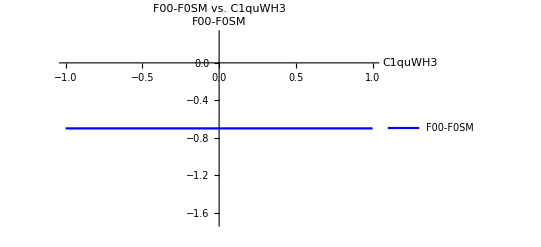

```mathematica
Plot[F00-F0SM,{C1quWH3,-1,1},PlotStyle->{Blue},AxesLabel->{"C1quWH3 ","F00-F0SM"},PlotLabel->"F00-F0SM vs. C1quWH3 ",PlotRange->All,PlotLegends->{"F00-F0SM"}]
```

```mathematica
C1quWH3=0.5;
```

```mathematica
F00
```

2.54252×10^-12

```mathematica
C1quWH3=-0.5;
```

```mathematica
F00
```

2.53756×10^-12

```mathematica
DecayWidth0
```

1.24621 Nc

```mathematica
DecayWidthTot
```

(4.91105×10^11+0. ⅈ) Nc

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
F00
```

1.34547×10^-102 (1.5432×10^90-6.53131×10^33 (4.32225×10^36+1.10418×10^21 (-1.08446×10^18-1.12043×10^25 Conjugate[C1qdWH3]))-1.10418×10^27 (1.35786×10^52-1.15223×10^9 (4.32225×10^36+1.10418×10^21 (-1.08446×10^18-1.12043×10^25 Conjugate[C1qdWH3]))-7.3914×10^46 (4.22288×10^15-1.94207×10^12 Conjugate[C1qdWH3]))-9.89565×10^72 (0.-1.78303×10^14 Conjugate[C1qdWH3])+1.53667×10^65 (4.22288×10^15-1.94207×10^12 Conjugate[C1qdWH3])+2.26962×10^12 (1.05546×10^15 (4.32225×10^36+1.10418×10^21 (-1.08446×10^18-1.12043×10^25 Conjugate[C1qdWH3]))+1.16541×10^36 (-1.08446×10^18-1.12043×10^25 Conjugate[C1qdWH3])+1.81991×10^49 (0.+2.67503×10^11 Conjugate[C1qdWH3])))

```mathematica
F0SM
```

0.698409

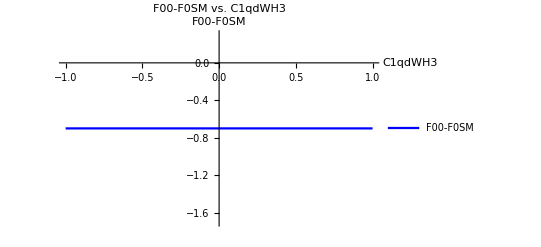

```mathematica
Plot[F00-F0SM,{C1qdWH3,-1,1},PlotStyle->{Blue},AxesLabel->{"C1qdWH3 ","F00-F0SM"},PlotLabel->"F00-F0SM vs. C1qdWH3 ",PlotRange->All,PlotLegends->{"F00-F0SM"}]
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
F00
```

1.34547×10^-102 (1.5432×10^90+1.53667×10^65 (4.22201×10^15+4 (2.17871×10^11+1.74634×10^13 (C2q2H4D+Conjugate[C2q2H4D])))-6.53131×10^33 (4.32225×10^36+1.10418×10^21 (0.+3.01316×10^13 (0.+179579. (0.+27455.5 C2q2H4D+27455.5 Conjugate[C2q2H4D]))+2.32549×10^15 (0.+4.7 (0.+8.11095×10^6 (C2q2H4D+Conjugate[C2q2H4D])))+8 (0.-60624.5 (2.23601×10^12+2.50045×10^13 (C2q2H4D+Conjugate[C2q2H4D])))))-1.10418×10^27 (1.35786×10^52-7.3914×10^46 (4.22201×10^15+4 (2.17871×10^11+1.74634×10^13 (C2q2H4D+Conjugate[C2q2H4D])))-1.15223×10^9 (4.32225×10^36+1.10418×10^21 (0.+3.01316×10^13 (0.+179579. (0.+27455.5 C2q2H4D+27455.5 Conjugate[C2q2H4D]))+2.32549×10^15 (0.+4.7 (0.+8.11095×10^6 (C2q2H4D+Conjugate[C2q2H4D])))+8 (0.-60624.5 (2.23601×10^12+2.50045×10^13 (C2q2H4D+Conjugate[C2q2H4D]))))))+2.26962×10^12 (1.81991×10^49 (0.-5.84956×10^12 (C2q2H4D+Conjugate[C2q2H4D]))+1.16541×10^36 (0.+3.01316×10^13 (0.+179579. (0.+27455.5 C2q2H4D+27455.5 Conjugate[C2q2H4D]))+2.32549×10^15 (0.+4.7 (0.+8.11095×10^6 (C2q2H4D+Conjugate[C2q2H4D])))+8 (0.-60624.5 (2.23601×10^12+2.50045×10^13 (C2q2H4D+Conjugate[C2q2H4D]))))+1.05546×10^15 (4.32225×10^36+1.10418×10^21 (0.+3.01316×10^13 (0.+179579. (0.+27455.5 C2q2H4D+27455.5 Conjugate[C2q2H4D]))+2.32549×10^15 (0.+4.7 (0.+8.11095×10^6 (C2q2H4D+Conjugate[C2q2H4D])))+8 (0.-60624.5 (2.23601×10^12+2.50045×10^13 (C2q2H4D+Conjugate[C2q2H4D]))))))-9.89565×10^72 (0.-2 (0.+1.94985×10^12 (C2q2H4D+Conjugate[C2q2H4D]))+52727.4 (0.+225.743 (0.+168871. (C2q2H4D+Conjugate[C2q2H4D])))-2049.58 (0.+59859.6 (0.-54910.9 Re[C2q2H4D]))))

```mathematica
F0SM
```

0.698409

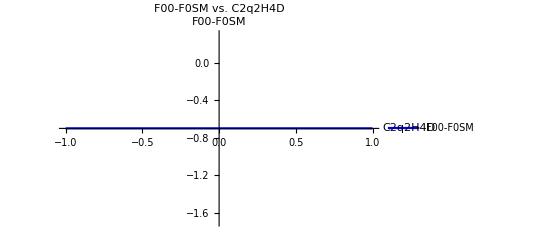

```mathematica
Plot[F00-F0SM,{C2q2H4D,-1,1},PlotStyle->{Blue},AxesLabel->{"C2q2H4D ","F00-F0SM"},PlotLabel->"F00-F0SM vs. C2q2H4D ",PlotRange->All,PlotLegends->{"F00-F0SM"}]
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D;
CudH4D=0;
```

```mathematica
F00
```

1.34547×10^-102 (1.5432×10^90-6.53131×10^33 (4.32225×10^36+1.10418×10^21 (0.+2.32549×10^15 (0.+4.7 (0.+8.11095×10^6 (C3q2H4D-Re[C3q2H4D])))+8 (0.-60624.5 (2.23601×10^12+2.50045×10^13 (C3q2H4D-Re[C3q2H4D])))+3.01316×10^13 (0.+179579. (0.+27455.5 C3q2H4D-27455.5 Re[C3q2H4D]))))-1.10418×10^27 (1.35786×10^52-1.15223×10^9 (4.32225×10^36+1.10418×10^21 (0.+2.32549×10^15 (0.+4.7 (0.+8.11095×10^6 (C3q2H4D-Re[C3q2H4D])))+8 (0.-60624.5 (2.23601×10^12+2.50045×10^13 (C3q2H4D-Re[C3q2H4D])))+3.01316×10^13 (0.+179579. (0.+27455.5 C3q2H4D-27455.5 Re[C3q2H4D]))))-7.3914×10^46 (4.22201×10^15+4 (2.17871×10^11+1.74634×10^13 (C3q2H4D-Re[C3q2H4D]))))+2.26962×10^12 (1.05546×10^15 (4.32225×10^36+1.10418×10^21 (0.+2.32549×10^15 (0.+4.7 (0.+8.11095×10^6 (C3q2H4D-Re[C3q2H4D])))+8 (0.-60624.5 (2.23601×10^12+2.50045×10^13 (C3q2H4D-Re[C3q2H4D])))+3.01316×10^13 (0.+179579. (0.+27455.5 C3q2H4D-27455.5 Re[C3q2H4D]))))+1.16541×10^36 (0.+2.32549×10^15 (0.+4.7 (0.+8.11095×10^6 (C3q2H4D-Re[C3q2H4D])))+8 (0.-60624.5 (2.23601×10^12+2.50045×10^13 (C3q2H4D-Re[C3q2H4D])))+3.01316×10^13 (0.+179579. (0.+27455.5 C3q2H4D-27455.5 Re[C3q2H4D])))+1.81991×10^49 (0.-5.84956×10^12 (C3q2H4D-Re[C3q2H4D])))+1.53667×10^65 (4.22201×10^15+4 (2.17871×10^11+1.74634×10^13 (C3q2H4D-Re[C3q2H4D])))-9.89565×10^72 (0.+52727.4 (0.+225.743 (0.+168871. (C3q2H4D-Re[C3q2H4D])))-2 (0.+1.94985×10^12 (C3q2H4D-Re[C3q2H4D]))-2049.58 (0.+59859.6 (0.+27455.5 (-C3q2H4D+Re[C3q2H4D])))))

```mathematica
F0SM
```

0.698409

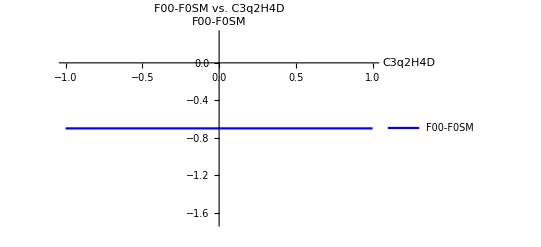

```mathematica
Plot[F00-F0SM,{C3q2H4D,-1,1},PlotStyle->{Blue},AxesLabel->{"C3q2H4D ","F00-F0SM"},PlotLabel->"F00-F0SM vs. C3q2H4D ",PlotRange->All,PlotLegends->{"F00-F0SM"}]
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D;
```

```mathematica
F00
```

1.34547×10^-102 (1.5432×10^90+1.53667×10^65 (4.22288×10^15-1.04936×10^12 Conjugate[CudH4D])-9.89565×10^72 (0.+52727.4 (0.+225.743 (0.-3.98935×10^6 Conjugate[CudH4D]))+1.65076×10^11 Conjugate[CudH4D]-2049.58 (0.+1.09403×10^11 Conjugate[CudH4D]))-6.53131×10^33 (4.32225×10^36+1.10418×10^21 (0.+3.01316×10^13 (0.-1.56645×10^11 Conjugate[CudH4D])+2.32549×10^15 (0.-9.00569×10^8 Conjugate[CudH4D])+8 (-1.35557×10^17+4.77125×10^16 Conjugate[CudH4D])))-1.10418×10^27 (1.35786×10^52-7.3914×10^46 (4.22288×10^15-1.04936×10^12 Conjugate[CudH4D])-1.15223×10^9 (4.32225×10^36+1.10418×10^21 (0.+3.01316×10^13 (0.-1.56645×10^11 Conjugate[CudH4D])+2.32549×10^15 (0.-9.00569×10^8 Conjugate[CudH4D])+8 (-1.35557×10^17+4.77125×10^16 Conjugate[CudH4D]))))+2.26962×10^12 (1.81991×10^49 (0.+2.47614×10^11 Conjugate[CudH4D])+1.16541×10^36 (0.+3.01316×10^13 (0.-1.56645×10^11 Conjugate[CudH4D])+2.32549×10^15 (0.-9.00569×10^8 Conjugate[CudH4D])+8 (-1.35557×10^17+4.77125×10^16 Conjugate[CudH4D]))+1.05546×10^15 (4.32225×10^36+1.10418×10^21 (0.+3.01316×10^13 (0.-1.56645×10^11 Conjugate[CudH4D])+2.32549×10^15 (0.-9.00569×10^8 Conjugate[CudH4D])+8 (-1.35557×10^17+4.77125×10^16 Conjugate[CudH4D])))))

```mathematica
F0SM
```

0.698409

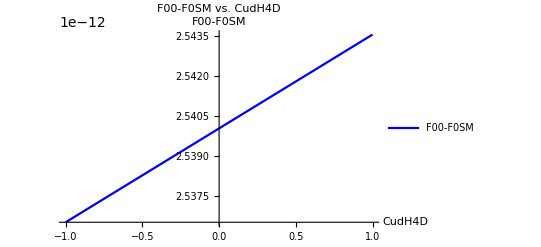

```mathematica
Plot[F0,{CudH4D,-1,1},PlotStyle->{Blue},AxesLabel->{"CudH4D ","F00-F0SM"},PlotLabel->"F00-F0SM vs. CudH4D ",PlotRange->All,PlotLegends->{"F00-F0SM"}]
```